```mathematica
nfw= rho0/(r/rs)/(1+r/rs)^2;
DSolve[{y''''[r]==-nfw-(4/r) y'''[r]},y[r],r]
```

{{y[r]→C[2]+r C[3]+r^2 C[4]-(6 r^2 rho0 rs^3+3 rho0 rs^5+2 C[1]-6 rho0 rs^3 (r+rs)^2 Log[r+rs])/(12 r)}}

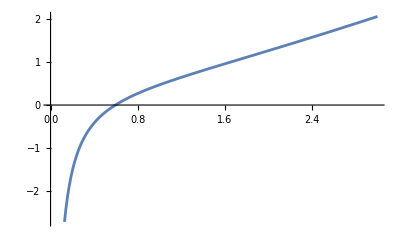

```mathematica
Plot[-(6 r^2 rho0 rs^3+3 rho0 rs^5+2 C[1]-6 rho0 rs^3 (r+rs)^2 Log[r+rs])/(12 r)/.{rs->1,rho0->1, C[1]->1 }, {r,0,3 }]
```

r-(12 r^2)/(12 r-6 r^2 rho0 rs^3-3 rho0 rs^5-2 C[1]+6 rho0 rs^3 (r+rs)^2 Log[r+rs])

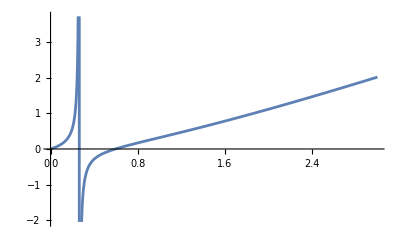

```mathematica
ϕ[r_]:=-(6 r^2 rho0 rs^3+3 rho0 rs^5+2 C[1]-6 rho0 rs^3 (r+rs)^2 Log[r+rs])/(12 r);
r D[ϕ[r]]/(1+ϕ[r])//FullSimplify
Plot[r-(12 r^2)/(12 r-6 r^2 rho0 rs^3-3 rho0 rs^5-2 C[1]+6 rho0 rs^3 (r+rs)^2 Log[r+rs])/.{rs->1,rho0->1, C[1]->1  }, {r,0,3 }]
```